# Log-Log Plots

```mathematica
(* Since Mathematica operates in a global environment, let's clear all that, so we're clean *)
Clear["Global`"];
(* Buttons to hide / show code *)
CloseAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];SetOptions[#,CellOpen->False]&/@cells;];

OpenAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];SetOptions[#,CellOpen->True]&/@cells;];

Row[{Button["Hide Code",SelectionEvaluate[CloseAllInputsCells[]]],Button["Show Code",SelectionEvaluate[OpenAllInputsCells[]]]}]
```

Hide CodeShow Code

```mathematica
prices=URLExecute["http://localhost:3110/api/v1/historical-price"];
vals=Select[Lookup[Values[prices][[1]],"USD"],#>0&];
```

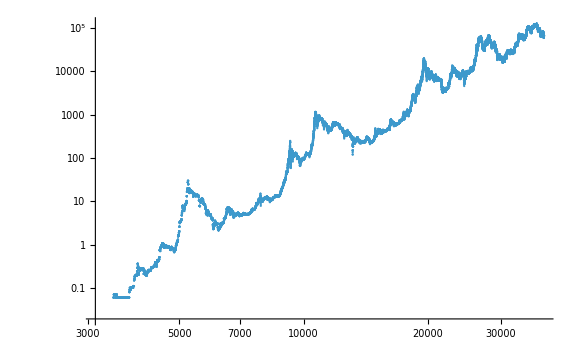

```mathematica
ListLogLogPlot[
{
Lookup[Values[prices][[1]],"USD"]
}
,GridLines->Automatic
,ImageMargins->20
,ImageSize->Large
]
```

```mathematica
Lookup[Values[prices][[1]],"USD"]
```